```mathematica
Clear["Global`*"]
```

```mathematica
(* Test of spectral density mapping, doesn't need to be run otherwise *)
SDtest[omega0_,etac_,Gamma_]:=Module[{ω0=omega0,ηc=etac,Γ=Gamma},
(*Γ=ω0^2/wc;*)
(*coupling strength and cut-off frequency in reaction coordinate*)
Λ=100000;
(*Mode frequency and spin-mode coupling*)
ω=ω0 //N;
κ=Sqrt[(π ηc ω0)/2];
γ=N[Γ/(2π ω0)];
Jrc[w_]:=γ w ;
(*check convergence*)
Jsb[v_]:=(ηc Γ ω0^2 v)/((ω0^2-v^2)^2+Γ^2 v^2);
J[v_,γ_,Λ_]:=γ v Exp[-v/Λ];
f[x_]:=ExpIntegralEi[x]-Exp[2x]ExpIntegralEi[-x];
Jcon[v_,γ_,Λ_]:=(4 κ^2 ω^2 J[v,γ,Λ])/((v^2-ω^2-2ω J[v,γ,Λ]f[v/Λ])^2+4 π^2 ω^2(J[v,γ,Λ])^2);
{concheck=Plot[{Jcon[v,γ,Λ],Jsb[v]},{v,0,400},PlotRange->{0,All},Frame->True],
Integrate[Jsb[v]/v,{v,0,∞}]}]
```

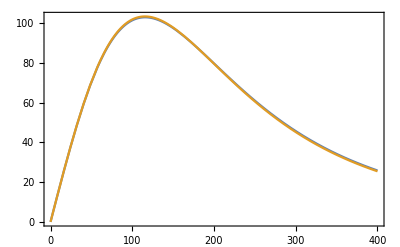
{-Graphics-,250.+0. ⅈ}

```mathematica
SDtest[200.0,N[500/π],200.0^2/100.0]
```

```mathematica
SteadySol[epsilon_,bias_,foerster_,phononbeta_,photonbeta_,omega0_,etac_,Gamma_,gammaEM_,statesnum_,choplevel_]:=Module[{ϵ=epsilon,ϵb=bias,V=foerster,β=phononbeta,βphoton=photonbeta,ω0=omega0,ηc=etac,Γ=Gamma,ΓEM=gammaEM,nstates=statesnum,ch=choplevel},
st=AbsoluteTime[];
Off[Eigensystem::arh];
Jsb[v_]:=(ηc Γ ω0^2 v)/((ω0^2-v^2)^2+Γ^2 v^2);
SBReorg=Integrate[Jsb[v]/v,{v,0,∞}];
ϵ1=ϵ+ϵb+SBReorg;ϵ2=ϵ+SBReorg;
(*Γ=ω0^2/wc;*)
ω=ω0 //N;
κ=Sqrt[(π ηc ω0)/2];
γ=N[Γ/(2π ω0)];
Jrc[w_]:=γ w ;

tensor[a___]:=KroneckerProduct[a];qeye[n_]:=Array[KroneckerDelta[#1,#2]&,{n,n}];dag[a_]:=ConjugateTranspose[a];

sx={{0,1},{1,0}};
sy={{0,-ⅈ},{ⅈ,0}};
sz={{1,0},{0,-1}};
sp=(sx+ⅈ sy)/2;
sm=(sx-ⅈ sy)/2;
c[a_,b_]:=a.b-b.a;
ac[a_,b_]:=a.b+b.a;
kp[a_,b_,c_,d_]:=KroneckerProduct[a,b,c,d];
out[a_,b_]:=Outer[Times,a,b];
id[n_]:=DiagonalMatrix[Table[1,{ii,1,n}]];
a[n_]:=Table[ Sqrt[i]*KroneckerDelta[i+1,j],{i,1,n},{j,1,n}]//N;
ad[n_]:=Table[ Sqrt[(i-1)]*KroneckerDelta[i,j+1],{i,1,n},{j,1,n}]//N;
zeromat[n_]:=ConstantArray[0,{4 n^2,4 n^2}];
occupation[ω_]:=1/(Exp[β ω]-1);
occupationphoton[ω_]:=1/(Exp[βphoton ω]-1);
(*define density operator*)
(*dens[n_]:=Array[Subscript[ρ, ##][t]&,{4 n^2,4 n^2}];*)
(*Hamiltonian*)
H[n_]:=SparseArray[ϵ1 KroneckerProduct[(id[2]+sz)/2,id[2],id[n],id[n]]+ϵ2 KroneckerProduct[id[2],(id[2]+sz)/2,id[n],id[n]]+V(KroneckerProduct[sp,sm,id[n],id[n]]+KroneckerProduct[sm,sp,id[n],id[n]])-κ KroneckerProduct[(id[2]+sz)/2,id[2],a[n]+ad[n],id[n]]-κ KroneckerProduct[id[2],(id[2]+sz)/2,id[n],a[n]+ad[n]]+ω KroneckerProduct[id[2],id[2],ad[n].a[n],id[n]]+ω KroneckerProduct[id[2],id[2],id[n],ad[n].a[n]]//N];
(*define intial conditions*)
(*initialmode[n_]:=(1/Tr[MatrixExp[-β ω ad[n].a[n]]]*MatrixExp[-β ω ad[n].a[n]]);
initialspin[n_]:=KroneckerProduct[{{0,0},{0,1}},{{0,0},{0,1}}];
initialdens[n_]:=KroneckerProduct[initialspin[n],initialmode[n],initialmode[n]]//Flatten;
initialddens[n_]:=KroneckerProduct[initialspin[n],initialmode[n],initialmode[n]];
initialcond[n_]:=Thread[Flatten[dens[n]/.t->0]==Flatten[KroneckerProduct[initialspin[n],initialmode[n],initialmode[n]]]];*)

n=nstates;
{vals,vecs}=Eigensystem[H[n]];
nvecs=Chop[ParallelMap[Normalize[#1]&,vecs],ch];
(*dHam=DiagonalMatrix[vals];*)
λ=Chop[ParallelTable[vals⟦i⟧-vals⟦j⟧,{i,1,Length[vals]},{j,1,Length[vals]}],10^-12];(*always chopped at 10^-12 *)
(*Φ[i_,j_]:=out[nvecs⟦i⟧,Conjugate[nvecs⟦j⟧]];
ph=Sum[Φ[i,j],{i,1,n},{j,1,n}];*)

qid=SparseArray[qeye[4 n^2]];
(*Pre multiplying super operator*)
spre[A_]:=SparseArray[tensor[A,qid]];
(*post multiplying super operator*)
spost[A_]:=SparseArray[tensor[qid,Transpose[A]]];
(*pre and post multiplication*)
sprepost[A_,B_]:=SparseArray[tensor[A,Transpose[B]]];
VecLind[A_]:=2*sprepost[A,dag[A]]-spre[dag[A].A]-spost[dag[A].A];

(*overlap between position and eigenstates*)
X1=SparseArray[Chop[ParallelTable[nvecs⟦i⟧.kp[id[2],id[2],a[n]+ad[n],id[n]].nvecs⟦j⟧,{i,1,Length[vals]},{j,1,Length[vals]}],ch]];
X2=SparseArray[Chop[ParallelTable[nvecs⟦i⟧.kp[id[2],id[2],id[n],a[n]+ad[n]].nvecs⟦j⟧,{i,1,Length[vals]},{j,1,Length[vals]}],ch]];
χ1=SparseArray[Chop[ParallelTable[π/2 γ If[λ⟦i,j⟧==0,2/β,λ⟦i,j⟧Coth[(β λ⟦i,j⟧)/2]]X1⟦i,j⟧,{i,1,Length[vals]},{j,1,Length[vals]}],ch]];
χ2=SparseArray[Chop[ParallelTable[π/2 γ If[λ⟦i,j⟧==0,2/β,λ⟦i,j⟧Coth[(β λ⟦i,j⟧)/2]]X2⟦i,j⟧,{i,1,Length[vals]},{j,1,Length[vals]}],ch]];
Ξ1=SparseArray[Chop[ParallelTable[π/2 Jrc[λ⟦i,j⟧]nvecs⟦i⟧.kp[id[2],id[2],a[n]+ad[n],id[n]].nvecs⟦j⟧,{i,1,Length[vals]},{j,1,Length[vals]}],ch]];
Ξ2=SparseArray[Chop[ParallelTable[π/2 Jrc[λ⟦i,j⟧]nvecs⟦i⟧.kp[id[2],id[2],id[n],a[n]+ad[n]].nvecs⟦j⟧,{i,1,Length[vals]},{j,1,Length[vals]}],ch]];

αEM=ΓEM/(2π ϵ1);
Jem[ω_]:=αEM ω;
δ=ϵ2/ϵ1;
A1=SparseArray[Chop[(kp[sp,id[2],id[n],id[n]]+δ kp[id[2],sp,id[n],id[n]]),ch]];
A2=SparseArray[Chop[(kp[sm,id[2],id[n],id[n]]+δ kp[id[2],sm,id[n],id[n]]),ch]];
A1eig=SparseArray[Chop[nvecs.A1.ConjugateTranspose[nvecs],ch]];
A2eig=SparseArray[Chop[nvecs.A2.ConjugateTranspose[nvecs],ch]];A1abs=SparseArray[Chop[ConjugateTranspose[nvecs].ParallelTable[π If[λ⟦i,j⟧==0,1/2 αEM/βphoton,HeavisideTheta[λ⟦i,j⟧] Jem[λ⟦i,j⟧] occupationphoton[λ⟦i,j⟧]]A1eig⟦i,j⟧,{i,1,Length[vals]},{j,1,Length[vals]}].nvecs,ch]];A1emit=SparseArray[Chop[ConjugateTranspose[nvecs].ParallelTable[π If[λ⟦i,j⟧==0,1/2 αEM/βphoton,HeavisideTheta[λ⟦i,j⟧] Jem[λ⟦i,j⟧] (1+occupationphoton[λ⟦i,j⟧])]A1eig⟦i,j⟧,{i,1,Length[vals]},{j,1,Length[vals]}].nvecs,ch]];
A2abs=SparseArray[Chop[ConjugateTranspose[nvecs].ParallelTable[π If[λ⟦i,j⟧==0,1/2 αEM/βphoton,HeavisideTheta[-λ⟦i,j⟧] Jem[-λ⟦i,j⟧] occupationphoton[-λ⟦i,j⟧]]A2eig⟦i,j⟧,{i,1,Length[vals]},{j,1,Length[vals]}].nvecs,ch]];
A2emit=SparseArray[Chop[ConjugateTranspose[nvecs].ParallelTable[π If[λ⟦i,j⟧==0,1/2 αEM/βphoton,HeavisideTheta[-λ⟦i,j⟧] Jem[-λ⟦i,j⟧](1+ occupationphoton[-λ⟦i,j⟧])]A2eig⟦i,j⟧,{i,1,Length[vals]},{j,1,Length[vals]}].nvecs,ch]];

ℒphoton=SparseArray[Chop[-spre[A1.A2emit]+sprepost[A2emit,A1]-spost[A2abs.A1]+sprepost[A1,A2abs]-spre[A2.A1abs]+sprepost[A1abs,A2]-spost[A1emit.A2]+sprepost[A2,A1emit],ch]];

HDimer=ϵ1 KroneckerProduct[(id[2]+sz)/2,id[2]]+ϵ2 KroneckerProduct[id[2],(id[2]+sz)/2]+V(KroneckerProduct[sp,sm]+KroneckerProduct[sm,sp]);
thermal=SparseArray[MatrixExp[-βphoton HDimer]/Tr[MatrixExp[-βphoton HDimer]]];

(*thermal=SparseArray[MatrixExp[-βphoton H[n]]/Tr[MatrixExp[-βphoton H[n]]]];*)

iX1=SparseArray[Chop[Inverse[vecs].X1.vecs,ch]];
iχ1=SparseArray[Chop[Inverse[vecs].χ1.vecs,ch]];
iΞ1=SparseArray[Chop[Inverse[vecs].Ξ1.vecs,ch]];
iX2=SparseArray[Chop[Inverse[vecs].X2.vecs,ch]];
iχ2=SparseArray[Chop[Inverse[vecs].χ2.vecs,ch]];
iΞ2=SparseArray[Chop[Inverse[vecs].Ξ2.vecs,ch]];

Louv=SparseArray[With[{Ham=H[n]},Chop[-ⅈ(spre[Ham]-spost[Ham])-(spre[iX1.iχ1]-sprepost[iX1,iχ1]-sprepost[iχ1,iX1]+spost[iχ1.iX1])+(spre[iX1.iΞ1]+sprepost[iX1,iΞ1]-sprepost[iΞ1,iX1]-spost[iΞ1.iX1])-(spre[iX2.iχ2]-sprepost[iX2,iχ2]-sprepost[iχ2,iX2]+spost[iχ2.iX2])+(spre[iX2.iΞ2]+sprepost[iX2,iΞ2]-sprepost[iΞ2,iX2]-spost[iΞ2.iX2])+ℒphoton,ch]]];

dsolss=With[{runorm=Partition[Eigenvectors[Louv,-1(*,Method->{"Arnoldi","Tolerance"->10^-8,"MaxIterations"->6000,"Shift"->10^-15}*)]⟦1⟧,4 n^2]},Chop[runorm/Tr[runorm],ch]];

(*sz1expecss=Chop[Tr[kp[sz,id[2],id[n],id[n]].(dsolss)],ch];
sx1expecss=Chop[Tr[kp[sx,id[2],id[n],id[n]].(dsolss)],ch];
numb1ss=Chop[Tr[kp[id[2],id[2],ad[n].a[n],id[n]].(dsolss)],ch];
sz2expecss=Chop[Tr[kp[id[2],sz,id[n],id[n]].(dsolss)],ch];
sx2expecss=Chop[Tr[kp[id[2],sx,id[n],id[n]].(dsolss)],ch];
numb2ss=Chop[Tr[kp[id[2],id[2],id[n],ad[n].a[n]].(dsolss)],ch];
sp1sm2expecss=Chop[Tr[kp[sp,sm,id[n],id[n]].(dsolss)],ch];
sm1sp2expecss=Chop[Tr[kp[sm,sp,id[n],id[n]].(dsolss)],ch];*)
site1pop=Chop[Tr[tensor[(id[2]+sz)/2,id[2],id[n],id[n]].dsolss],ch];
site2pop=Chop[Tr[tensor[id[2],(id[2]+sz)/2,id[n],id[n]].dsolss],ch];
site1proj=Chop[Tr[tensor[(id[2]+sz)/2,(id[2]-sz)/2,id[n],id[n]].dsolss],ch];
site2proj=Chop[Tr[tensor[(id[2]-sz)/2,(id[2]+sz)/2,id[n],id[n]].dsolss],ch];

site1popthermal=Chop[Tr[tensor[(id[2]+sz)/2,id[2](*,id[n],id[n]*)].thermal],ch];
site2popthermal=Chop[Tr[tensor[id[2],(id[2]+sz)/2(*,id[n],id[n]*)].thermal],ch];
site1projthermal=Chop[Tr[tensor[(id[2]+sz)/2,(id[2]-sz)/2(*,id[n],id[n]*)].thermal],ch];
site2projthermal=Chop[Tr[tensor[(id[2]-sz)/2,(id[2]+sz)/2(*,id[n],id[n]*)].thermal],ch];


(*HDimer=ϵ1 KroneckerProduct[(id[2]+sz)/2,id[2]]+ϵ2 KroneckerProduct[id[2],(id[2]+sz)/2]+V(KroneckerProduct[sp,sm]+KroneckerProduct[sm,sp]);*)

doublepop=Chop[Tr[tensor[out[Eigenvectors[HDimer]⟦1⟧,Eigenvectors[HDimer]⟦1⟧],id[n],id[n]].dsolss],ch];
e2pop=Chop[Tr[tensor[out[Eigenvectors[HDimer]⟦2⟧,Eigenvectors[HDimer]⟦2⟧],id[n],id[n]].dsolss],ch];
e1pop=Chop[Tr[tensor[out[Eigenvectors[HDimer]⟦3⟧,Eigenvectors[HDimer]⟦3⟧],id[n],id[n]].dsolss],ch];
e0pop=Chop[Tr[tensor[out[Eigenvectors[HDimer]⟦4⟧,Eigenvectors[HDimer]⟦4⟧],id[n],id[n]].dsolss],ch];
e21coh=Chop[Tr[tensor[out[Eigenvectors[HDimer]⟦2⟧,Eigenvectors[HDimer]⟦3⟧],id[n],id[n]].dsolss],ch];
e12coh=Chop[Tr[tensor[out[Eigenvectors[HDimer]⟦3⟧,Eigenvectors[HDimer]⟦2⟧],id[n],id[n]].dsolss],ch];

doublepopthermal=Chop[Tr[(*tensor[*)out[Eigenvectors[HDimer]⟦1⟧,Eigenvectors[HDimer]⟦1⟧](*,id[n],id[n]]*).thermal],ch];
e2popthermal=Chop[Tr[(*tensor[*)out[Eigenvectors[HDimer]⟦2⟧,Eigenvectors[HDimer]⟦2⟧](*,id[n],id[n]]*).thermal],ch];
e1popthermal=Chop[Tr[(*tensor[*)out[Eigenvectors[HDimer]⟦3⟧,Eigenvectors[HDimer]⟦3⟧](*,id[n],id[n]]*).thermal],ch];
e0popthermal=Chop[Tr[(*tensor[*)out[Eigenvectors[HDimer]⟦4⟧,Eigenvectors[HDimer]⟦4⟧](*,id[n],id[n]]*).thermal],ch];
e21cohthermal=Chop[Tr[(*tensor[*)out[Eigenvectors[HDimer]⟦2⟧,Eigenvectors[HDimer]⟦3⟧](*,id[n],id[n]]*).thermal],ch];
e12cohthermal=Chop[Tr[(*tensor[*)out[Eigenvectors[HDimer]⟦3⟧,Eigenvectors[HDimer]⟦2⟧](*,id[n],id[n]]*).thermal],ch];
en=AbsoluteTime[];
(*Print["Steady-state solution took ", en-st," seconds"];*)
(*Export[TextString[Row[{Directory[],"/Data/RC_EM_Dimer/","ssn",nstates,".dat"}]],dsolss];*)
{site1proj,site1projthermal,site2proj,site2projthermal,e0pop,e0popthermal,e1pop,e1popthermal,e2pop,e2popthermal,doublepop,doublepopthermal,Abs[e12coh],Abs[e12cohthermal],site1proj+site2proj+e0pop+doublepop(*,e21coh*)}]
```

```mathematica
(*order of inputs is given by SteadySol[epsilon_,bias_,foerster_,phononbeta_,photonbeta_,omega0_,etac_,Gamma_,gammaEM_,statesnum_,choplevel_]*)
```

```mathematica
SteadySol[1.4 8065.5,0.001 8065.5,0.001 8065.5,1/(0.695 300),1/(0.695 6000),200.0,N[0.0/π],200.0^2/100.0,5.309 10^-3,4,10^-12]
```

{0.0584984,0.0584984,0.0586116,0.0586116,0.878989,0.878989,0.0586816,0.0586816,0.0584284,0.0584284,0.0039007,0.0039007,0,0,1.}

```mathematica
alphatable4states=Table[{α,SteadySol[1.4 8065.5,0.0 8065.5,0.001 8065.5,1/(0.695 300),1/(0.695 6000),200.0,N[α/π],200.0^2/100.0,5.309 10^-3,4,10^-7]},{α,0.01,1000,10}];
```

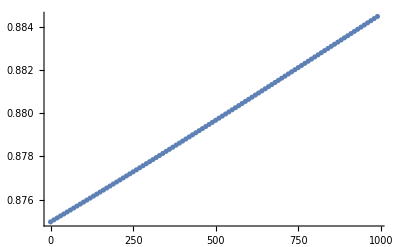

```mathematica
ListPlot[Transpose[Join[{alphatable4states⟦All,1⟧},{alphatable4states⟦All,2,1⟧}]]]
```

```mathematica
ListPlot[{Transpose[Join[{alphatable4states⟦All,1⟧},{alphatable4states⟦All,2,2⟧}]],Transpose[Join[{alphatable4states⟦All,1⟧},{alphatable4states⟦All,2,3⟧}]]},Joined->True,PlotStyle->Dashed,Frame->True,FrameLabel->{"πα","Eigenstate population"}]
```

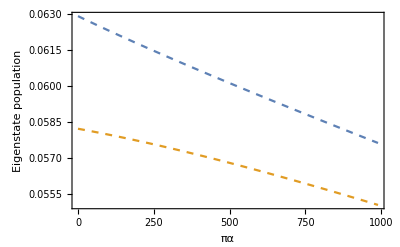
```mathematica
fivestates=-Graphics-
```

-Graphics-

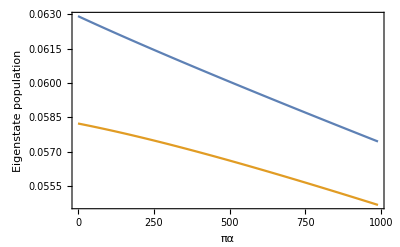
```mathematica
fourstates=-Graphics-
```

-Graphics-

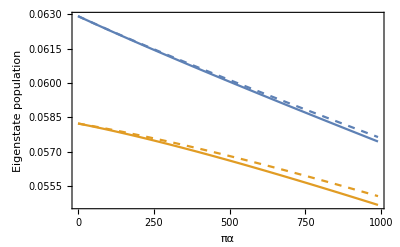

```mathematica
Show[fourstates,fivestates]
```

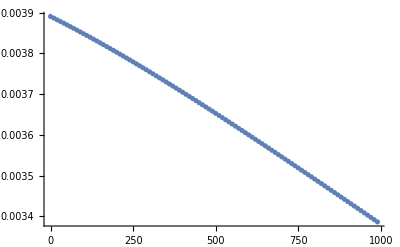

```mathematica
ListPlot[Transpose[Join[{alphatable4states⟦All,1⟧},{alphatable4states⟦All,2,4⟧}]]]
```

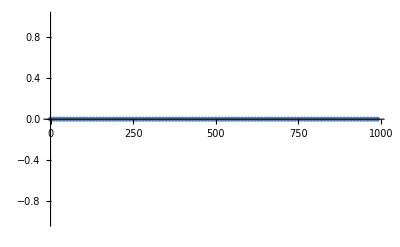

```mathematica
ListPlot[Transpose[Join[{alphatable4states⟦All,1⟧},{alphatable4states⟦All,2,5⟧}]]]
```

```mathematica
convergencetab=Table[{num,SteadySol[1.4 8065.5,0.0 8065.5,0.001 8065.5,1/(0.695 300),1/(0.695 6000),200.0,N[1000.0/π],200.0^2/100.0,5.309 10^-3,num,10^-7]},{num,2,8,1}]
```

{{2,{0.886446,0.0568864,0.0534371,0.00323008,0}},{3,{0.8854,0.0571567,0.0541268,0.00331624,0}},{4,{0.884591,0.0573918,0.0546361,0.00338113,0}},{5,{0.883956,0.0575888,0.0550237,0.00343123,0}},{6,{0.883458,0.0577517,0.0553206,0.00347001,0}},{7,{0.88307,0.0578837,0.0555466,0.00349976,0}},{8,{0.882774,0.0579879,0.0557162,0.00352218,0}}}

```mathematica
(* Command Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,i⟧}]] puts data in more convenient form i.e. pairs of points (n,value) for whichever observable is chosen through i *)
Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,1⟧}]]
```

{{2,0.886446},{3,0.8854},{4,0.884591},{5,0.883956},{6,0.883458},{7,0.88307},{8,0.882774}}

```mathematica
(* Fitted values *)
e0popfit=cc/.FindFit[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,1⟧}]], aa Exp[-bb x]+cc,{aa,bb,cc},x,AccuracyGoal->7]
e1popfit=cc/.FindFit[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,2⟧}]], aa Exp[-bb x]+cc,{aa,bb,cc},x,AccuracyGoal->7]
e2popfit=cc/.FindFit[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,3⟧}]], aa Exp[-bb x]+cc,{aa,bb,cc},x,AccuracyGoal->7]
doublepopfit=cc/.FindFit[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,4⟧}]], aa Exp[-bb x]+cc,{aa,bb,cc},x,AccuracyGoal->7]
Abse12cohfit=cc/.FindFit[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,5⟧}]], aa Exp[-bb x]+cc,{aa,bb,cc},x,AccuracyGoal->7]
```

0.881703

0.058541

0.0562409

0.00359659

0.

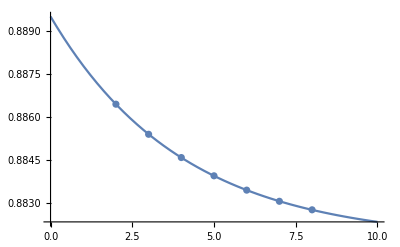

```mathematica
Show[Plot[(aa Exp[-bb xx]+cc)/.FindFit[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,1⟧}]], aa Exp[-bb x]+cc,{aa,bb,cc},x,AccuracyGoal->7],{xx,0,10}],ListPlot[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,1⟧}]]]]
```

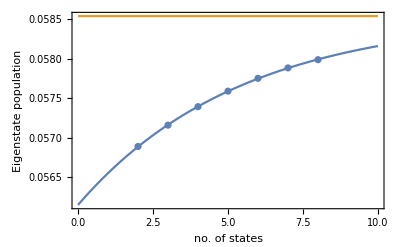

```mathematica
Show[Plot[{(aa Exp[-bb xx]+cc)/.FindFit[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,2⟧}]], aa Exp[-bb x]+cc,{aa,bb,cc},x,AccuracyGoal->7],e1popfit},{xx,0,10}],ListPlot[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,2⟧}]]],Frame->True,FrameLabel->{"no. of states","Eigenstate population"}]
```

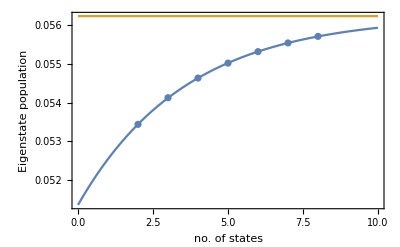

```mathematica
Show[Plot[{(aa Exp[-bb xx]+cc)/.FindFit[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,3⟧}]], aa Exp[-bb x]+cc,{aa,bb,cc},x,AccuracyGoal->7],e2popfit},{xx,0,10}],ListPlot[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,3⟧}]]],Frame->True,FrameLabel->{"no. of states","Eigenstate population"}]
```

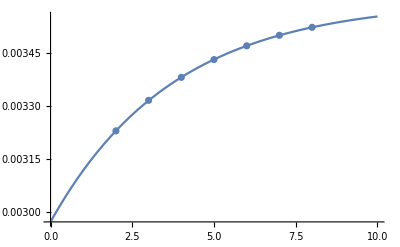

```mathematica
Show[Plot[(aa Exp[-bb xx]+cc)/.FindFit[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,4⟧}]], aa Exp[-bb x]+cc,{aa,bb,cc},x,AccuracyGoal->7],{xx,0,10}],ListPlot[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,4⟧}]]]]
```

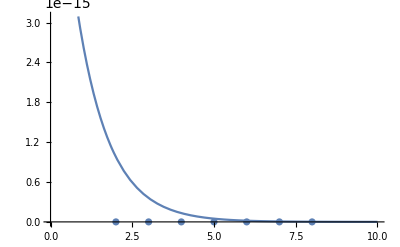

```mathematica
Show[Plot[(aa Exp[-bb xx]+cc)/.FindFit[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,5⟧}]], aa Exp[-bb x]+cc,{aa,bb,cc},x,AccuracyGoal->7],{xx,0,10}],ListPlot[Transpose[Join[{convergencetab⟦All,1⟧},{convergencetab⟦All,2,5⟧}]]]]
```